```mathematica
a=Exp[4Pi I/5];
b=Exp[-3Pi I/5];
R=({{a, 0}, {0, b}});
ϕ=GoldenRatio;
F=({{ϕ^-1, ϕ^(-1/2)}, {ϕ^(-1/2), -ϕ^-1}});
x=Inverse[F].R.F;
x11=x[[1,1]];
x12=x[[1,2]];
x21=x[[2,1]];
x22=x[[2,2]];
```

```mathematica
ComplexToPolar[z_]/;z∈Complexes:=Module[{w},w=FullSimplify[z];FullSimplify[Abs[w]]Exp[I Arg[w]]];
PlotComplex[data_]:=Module[{p},
p=ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},AspectRatio->1,Frame->True,PlotStyle->Directive[Red,PointSize[.025]]];Show[p,Graphics[{Thickness[0.003],Circle[{0,0},1]}]]
]
ShowEV[A_]:=Module[{ev,evNoDupes,p},
ev=Eigenvalues[A];
Print[ev];
(*evNoDupes=DeleteDuplicates[ev];*)
(*Print[Length[evNoDupes]," of ",Length[ev]," distinct ",ComplexToPolar[evNoDupes]," = ",N[evNoDupes]];*)
PlotComplex[ev]
];
```

2 of 5 distinct {ⅇ^((4 ⅈ π)/5),ⅇ^(-(3 ⅈ π)/5)} = {-0.809017+0.587785 ⅈ,-0.309017-0.951057 ⅈ}

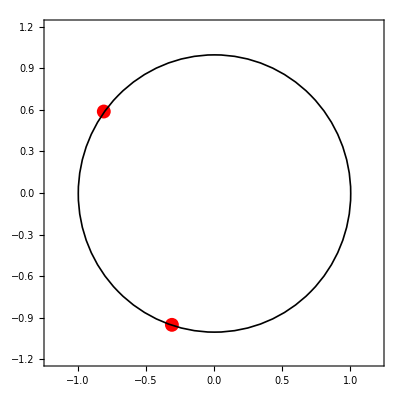

```mathematica
(* p=0 *)
ρ2σ1=({{a, 0, 0, 0, 0}, {0, b, 0, 0, 0}, {0, 0, b, 0, 0}, {0, 0, 0, x11, x12}, {0, 0, 0, x21, x22}});
ShowEV[ρ2σ1]
```

{0.809017-0.587785 ⅈ,-0.809017+0.587785 ⅈ,0.809017-0.587785 ⅈ,0.809017+0.587785 ⅈ,0.809017-0.587785 ⅈ,0.809017+0.587785 ⅈ,-0.809017+0.587785 ⅈ,-0.809017+0.587785 ⅈ}

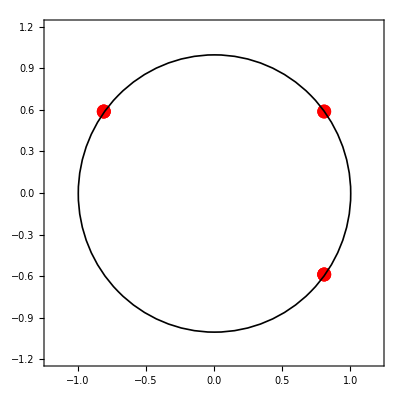

0.809017+0.587785 ⅈ

```mathematica
(* p=1 *)
ρ3σ2=({{b, 0, 0, 0, 0, 0, 0, 0}, {0, a, 0, 0, 0, 0, 0, 0}, {0, 0, b, 0, 0, 0, 0, 0}, {0, 0, 0, x11, x12, 0, 0, 0}, {0, 0, 0, x21, x22, 0, 0, 0}, {0, 0, 0, 0, 0, x11, 0, x12}, {0, 0, 0, 0, 0, 0, b, 0}, {0, 0, 0, 0, 0, x21, 0, x22}});
ρ3σ1=({{b, 0, 0, 0, 0, 0, 0, 0}, {0, x11, x12, 0, 0, 0, 0, 0}, {0, x21, x22, 0, 0, 0, 0, 0}, {0, 0, 0, a, 0, 0, 0, 0}, {0, 0, 0, 0, b, 0, 0, 0}, {0, 0, 0, 0, 0, b, 0, 0}, {0, 0, 0, 0, 0, 0, x11, x21}, {0, 0, 0, 0, 0, 0, x21, x22}});
ShowEV[ρ3σ1.ρ3σ2.ρ3σ1//N]
Det[ρ3σ1.ρ3σ2.ρ3σ1]//N
```

{-0.809017+0.587785 ⅈ,0.809017-0.587785 ⅈ,-0.309017-0.951057 ⅈ,-0.809017+0.587785 ⅈ,0.809017+0.587785 ⅈ}

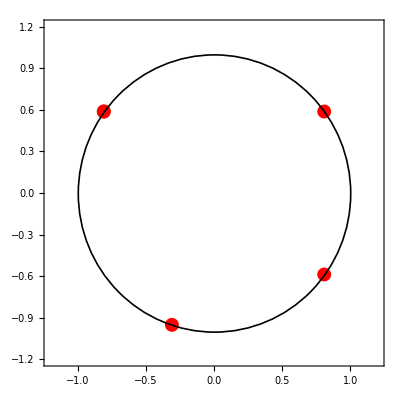

```mathematica
(* p=2 *)
ρ4σ1=({{x11, 0, 0, x12, 0}, {0, x11, 0, 0, x12}, {0, 0, b, 0, 0}, {x21, 0, 0, x22, 0}, {0, x21, 0, 0, x22}});
ρ4σ2=({{a, 0, 0, 0, 0}, {0, b, 0, 0, 0}, {0, 0, b, 0, 0}, {0, 0, 0, x11, x12}, {0, 0, 0, x21, x22}});
ρ4σ3=({{x11, x12, 0, 0, 0}, {x21, x22, 0, 0, 0}, {0, 0, x11, 0, x12}, {0, 0, 0, b, 0}, {0, 0, x21, 0, x22}});
ShowEV[ρ4σ1.ρ4σ2.ρ4σ3.ρ4σ2.ρ4σ1//N]
```

2 of 2 distinct {-0.809017+0.587785 ⅈ,0.809017+0.587785 ⅈ} = {-0.809017+0.587785 ⅈ,0.809017+0.587785 ⅈ}

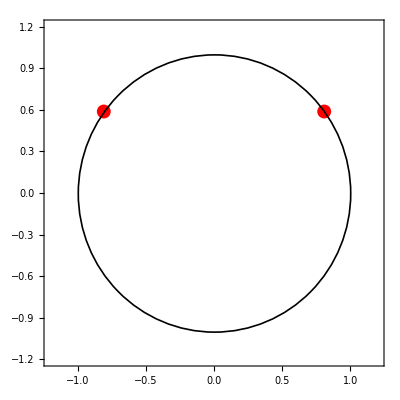

3 of 3 distinct {-0.309017-0.951057 ⅈ,-0.809017+0.587785 ⅈ,0.809017-0.587785 ⅈ} = {-0.309017-0.951057 ⅈ,-0.809017+0.587785 ⅈ,0.809017-0.587785 ⅈ}

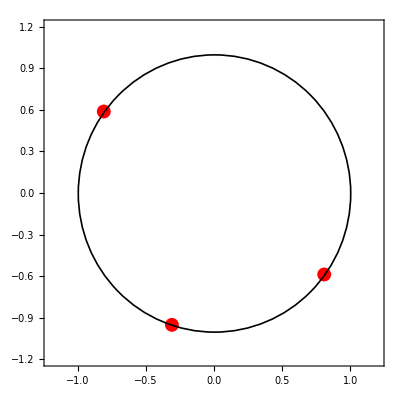

```mathematica
(* p=2 *)
(* sector 11 *)
ShowEV[R.x.R.x.R//N]
(* sector τ1 *)
ShowEV[{{a,0,0},{0,b,0},{0,0,b}}.{{x11,0,x12},{0,b,0},{x21,0,x22}}.{{b,0,0},{0,x11,x12},{0,x21,x22}}.{{x11,0,x12},{0,b,0},{x21,0,x22}}.{{a,0,0},{0,b,0},{0,0,b}}//N]
```

4 of 5 distinct {-1.,1.,-1.,1.} = {-1.,1.,-1.,1.}

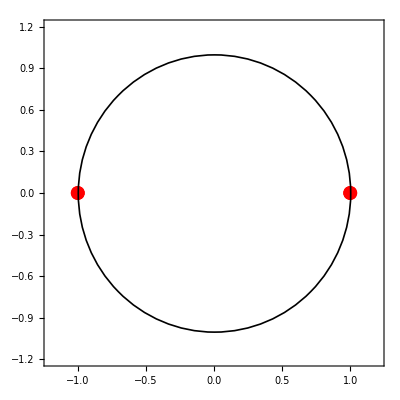

7 of 8 distinct {-1.,1.,-1.,1.,-1.,1.,-1.} = {-1.,1.,-1.,1.,-1.,1.,-1.}

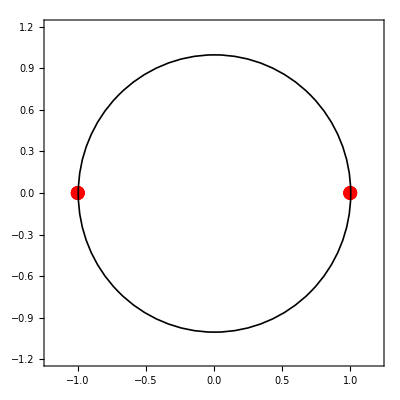

5 of 5 distinct {1.,-1.,1.,-1.,-1.} = {1.,-1.,1.,-1.,-1.}

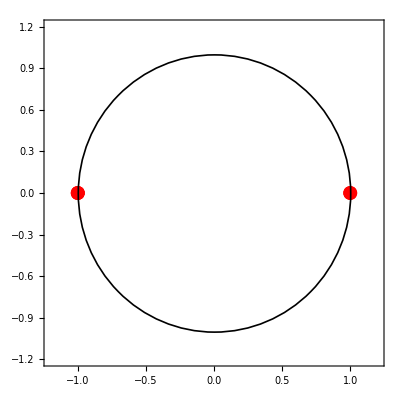

```mathematica
(* Zero energy braid *)
ShowEV[MatrixPower[ρ2σ1,5]//N]
ShowEV[MatrixPower[ρ3σ1.ρ3σ2.ρ3σ1,5]//N]
ShowEV[MatrixPower[ρ4σ1.ρ4σ2.ρ4σ3.ρ4σ2.ρ4σ1,5]//N]
```

```mathematica
MatrixPower[ρ2σ1,5]//N//MatrixForm
```

(1. | 0. | 0. | 0. | 0.
0. | -1. | 0. | 0. | 0.
0. | 0. | -1. | 0. | 0.
0. | 0. | 0. | -0.236068-4.996×10^-16 ⅈ | 0.971737+6.93889×10^-17 ⅈ
0. | 0. | 0. | 0.971737+1.249×10^-16 ⅈ | 0.236068-4.996×10^-16 ⅈ)

```mathematica
ρ2σ1//N//MatrixForm
```

(-0.809017+0.587785 ⅈ | 0. | 0. | 0. | 0.
0. | -0.309017-0.951057 ⅈ | 0. | 0. | 0.
0. | 0. | -0.309017-0.951057 ⅈ | 0. | 0.
0. | 0. | 0. | -0.5-0.363271 ⅈ | -0.242934+0.747674 ⅈ
0. | 0. | 0. | -0.242934+0.747674 ⅈ | -0.618034+5.55112×10^-17 ⅈ)

```mathematica
Eigenvalues[({{-0.2360679774997897, 0.9717365435132908}, {0.9717365435132909, 0.23606797749978942}})]
```

{-1.,1.}

```mathematica
x.R.x//N//MatrixForm
```

(-0.5+0.363271 ⅈ | -0.63601+0.462088 ⅈ
-0.63601+0.462088 ⅈ | 0.5-0.363271 ⅈ)

```mathematica
Sqrt[1-0.9717365435132909^2]
```

0.236068

```mathematica
ShowEV[R.x.R.x.R//N]
```

{-0.809017+0.587785 ⅈ,0.809017+0.587785 ⅈ}

-Graphics-

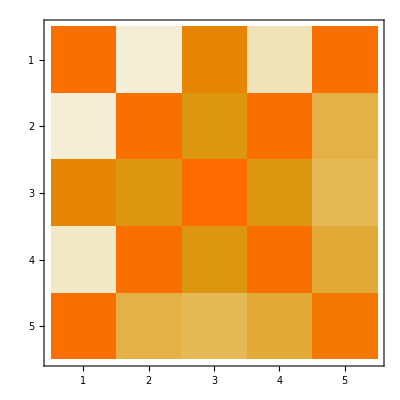

```mathematica
MatrixPlot[ρ4σ1.ρ4σ2.ρ4σ3.ρ4σ2.ρ4σ1//N//Abs]
```

```mathematica
Abs[ρ4σ1.ρ4σ2.ρ4σ3.ρ4σ2.ρ4σ1//N]//MatrixForm
```

(0.618034 | 6.20634×10^-17 | 0.485868 | 1.00074×10^-16 | 0.618034
6.20634×10^-17 | 0.618034 | 0.381966 | 0.618034 | 0.300283
0.485868 | 0.381966 | 0.618034 | 0.381966 | 0.300283
8.32667×10^-17 | 0.618034 | 0.381966 | 0.618034 | 0.300283
0.618034 | 0.300283 | 0.300283 | 0.300283 | 0.589512)